# Unanchored Double Pendulum Equations of Motion

An attempt.

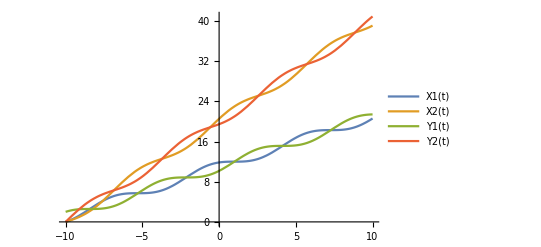

```mathematica
Needs["VariationalMethods`"]
MyNormSquared[{x_,y_}] := x^2+y^2
x1[t] ;(* first coordinate of link 1 *)
x2[t]; (* second coordinate of link 1 *)
theta1[t];
theta2[t];
(* Initial Conditions*)
t0 = -10;
Ix1 = x1[t0] == 0;
Ix1P= x1'[t0] == 1;
Ix2 =x2[t0] == 0;
Ix2P = x2'[t0] == 1;
It1 = theta1[t0] == 0;
It1P = theta1'[t0] == 1;
It2 = theta2[t0] == 0;
It2P = theta2'[t0] == 1;
InitialConditions = {Ix1,Ix1P,Ix2,Ix2P,It1,It1P,It2,It2P};
(**)
r1 = 1;
r2 = 1;
m1 = 1; 
m2 = 1;
J1 = 1;
J2 = 1;
x[t]= {x1[t], x2[t]};
theta[t] = {theta1[t],theta2[t]};
y1[t]=x1[t] + r1 Cos[theta1[t]] + r2 Cos[theta2[t]];(* first coordinate of link 2 *)
y2[t] = x2[t] + r1 Sin[theta1[t]]+r2 Sin[theta2[t]];(* second coordinate of link 2 *)
y[t] = {y1[t],y2[t]};

 KEx[t] = (1/2) m1 MyNormSquared[D[x[t],t]];
 KEy[t] = (1/2) m2  MyNormSquared[D[y[t],t]];
KErot[t] = (1/2) (J1 D[theta1[t],t]^2 + J2 D[theta2[t],t]^2);
 KET[t] = KEy[t] + KEx[t] + KErot[t];
 Lagrangian[t] = KET[t];
EOM1[t] = {D[D[Lagrangian[t],x1'[t]],t] - D[Lagrangian[t],x1[t]], D[D[Lagrangian[t],x2'[t]],t] - D[Lagrangian[t],x2[t]], D[D[Lagrangian[t],theta1'[t]],t] - D[Lagrangian[t],theta1[t]],D[D[Lagrangian[t],theta2'[t]],t] - D[Lagrangian[t],theta2[t]]};
EOM[t] = Simplify[EOM1[t]];
DSolve[EOM[t] == {0,0,0,0}, {x1[t],x2[t],theta1[t],theta2[t]},t];
Sol = NDSolve[{EOM[t] == {0,0,0,0},InitialConditions},{x1[t],x2[t],theta1[t],theta2[t]},{t,-10,10},Method->{"EquationSimplification"->"Solve"}];
Y1[t] = x1[t] + r1 Cos[theta1[t]] + r2 Cos[theta2[t]] /. Sol;
Y2[t] = x2[t] + r1 Sin[theta1[t]]+r2 Sin[theta2[t]]/. Sol;
X1[t] = x1[t] /. Sol;
X2[t] = x2[t] /. Sol;
Plot[{X1[t],X2[t],Y1[t],Y2[t]},{t,-10,10},PlotLegends-> "Expressions"]
```

```mathematica
Quit
Remove["Global`*"]
ClearAll
```

ClearAll